```mathematica
SetDirectory["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_charge"];
Needs["ErrorBarPlots`"];
Get["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_Demo/ErrorBarLogPlots.m"];
Get["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_Demo/ProtonFluxAnn.m"];
```

## AMS02-Experiment Error Bar Import

57

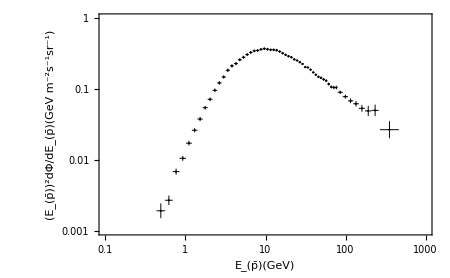

```mathematica
IError = Import[  "/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_Demo/Error_data_AMS02_Full.dat","Table",HeaderLines-> 1];
Length[IError]
IError1=Table[{IError[[i,1]],IError[[i,2]],(IError[[i,4]]-IError[[i,3]])/2,(IError[[i,6]]-IError[[i,5]])/2},{i,1,Length[IError]}];
IError2=IError1/.{x_,y_,z_,k_}->{{x,y},ErrorBar[z,k]};
ErroPlot1=ErrorListLogLogPlot[IError2,Frame->True,Axes->False,PlotRange->{{10^-1,10^3},{10^-3,1}}, ErrorBarFunction->Automatic,ImageSize->450,PlotStyle->{Black,AbsolutePointSize[1.5],AbsoluteThickness[0.7]},FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

## Get Background(BG)

393

InterpolatingFunction[…]

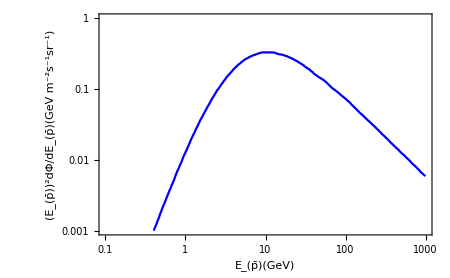

```mathematica
BG00=Import["/Users/sinbi/desktop/AMS02.csv","CSV","HearderLines"->1];
BG01=Table[BG00[[i,All]],{i,7,399}];
Length[BG01]
ifBG0=Interpolation[BG01]
BGPlot=ListLogLogPlot[ifBG0,Joined->True,Axes->False,Frame->True,PlotRange->{{10^-1,10^3},{10^-3,1}},ImageSize->450,PlotStyle->{Blue},FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

## Dark Matter(DM)

```mathematica
GeV=1;
topm=173.0GeV;
```

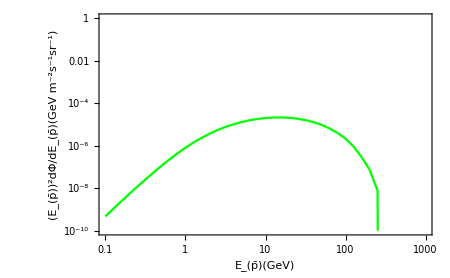

```mathematica
primaryτc="τ";
haloτc="NFW";
propagationτc="MED";
mDMτc=300GeV;
σvτc=10^-26;
Eγτc=10^lEγ;
Poτc=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryτc, haloτc, propagationτc][mDMτc, σvτc,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDτc=ListLogLogPlot[Poτc,PlotRange->{{10^-1,10^3},{10^-10,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

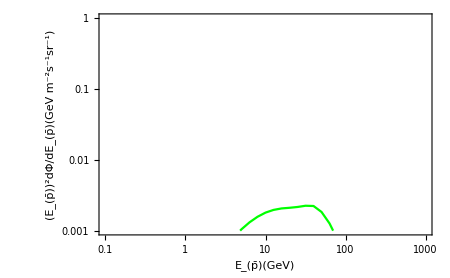

```mathematica
primarybc="b";
halobc="NFW";
propagationbc="MED";
mDMbc=300GeV;
σvbc=3× (1/3)^2×σvτc;
Eγbc=10^lEγ;
Pobc=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primarybc, halobc, propagationbc][mDMbc, σvbc,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDbc=ListLogLogPlot[Pobc,PlotRange->{{10^-1,10^3},{10^-3,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

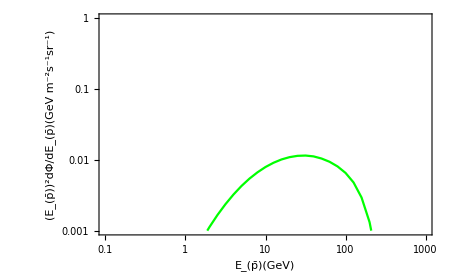

```mathematica
primarycc="c";
halocc="NFW";
propagationcc="MED";
mDMcc=300GeV;
σvcc=3× (2/3)^2×σvτc;
Eγcc=10^lEγ;
Pocc=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primarycc, halocc, propagationcc][mDMcc, σvcc,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDcc=ListLogLogPlot[Pocc,PlotRange->{{10^-1,10^3},{10^-3,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

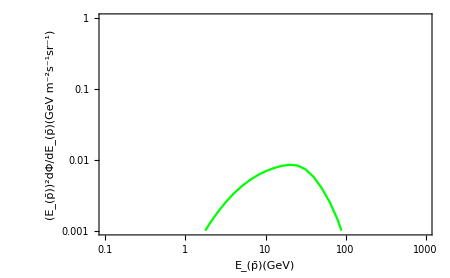

```mathematica
primarytc="t";
halotc="NFW";
propagationtc="MED";
mDMtc=300GeV;
σvtc=3× (2/3)^2×σvτc;
Eγtc=10^lEγ;
Potc=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primarytc, halotc, propagationtc][mDMtc, σvtc,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDtc=ListLogLogPlot[Potc,Joined->True,PlotRange->{{10^-1,10^3},{10^-3,1}},PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

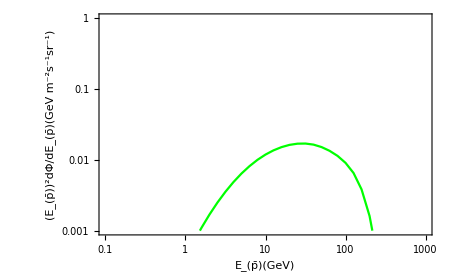

```mathematica
primaryqc="q";
haloqc="NFW";
propagationqc="MED";
mDMqc=300GeV;
σvqc=3× ((2/3)^2+(1/3)^2+(1/3)^2)×σvτc;
Eγqc=10^lEγ;
Poqc=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryqc, haloqc, propagationqc][mDMqc, σvqc,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDqc=ListLogLogPlot[Poqc,PlotRange->{{10^-1,10^3},{10^-3,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

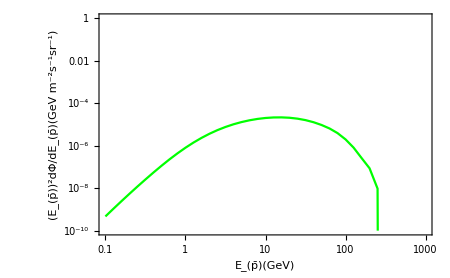

```mathematica
primaryec="e";
haloec="NFW";
propagationec="MED";
mDMec=300GeV;
σvec=σvτc;
Eγec=10^lEγ;
Poec=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryec, haloec, propagationec][mDMec, σvec,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDec=ListLogLogPlot[Poec,PlotRange->{{10^-1,10^3},{10^-10,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

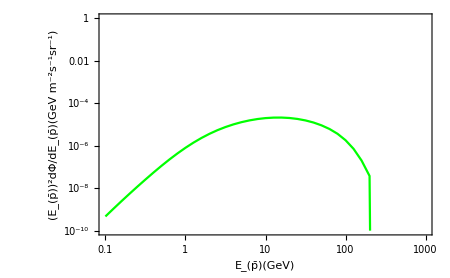

```mathematica
primaryμc="μ";
haloμc="NFW";
propagationμc="MED";
mDMμc=300GeV;
σvμc=σvτc;
Eγμc=10^lEγ;
Poμc=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryμc, haloμc, propagationμc][mDMμc, σvμc,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDμc=ListLogLogPlot[Poμc,PlotRange->{{10^-1,10^3},{10^-10,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

```mathematica
Length[Poμc];
Length[Poec];
Length[Potc];
Length[Poτc];
Length[Pocc];
Length[Pobc];
Length[Poqc];
```

```mathematica
ifPoc1=Table[{Poμc[[i,1]],(Poμc[[i,2]]+Poec[[i,2]]+Potc[[i,2]]+Poτc[[i,2]]+Pocc[[i,2]]+Pobc[[i,2]]+Poqc[[i,2]])},{i,1,Length[Poμc]}];
Length[ifPoc1]
ifPoc1f=Interpolation[ifPoc1]
```

401

InterpolatingFunction[…]

```mathematica
ifPoc2=Table[{Poμc[[i,1]],(Poμc[[i,2]]+Poec[[i,2]]+Poτc[[i,2]]+Pocc[[i,2]]+Pobc[[i,2]]+Poqc[[i,2]])},{i,1,Length[Poμc]}];
Length[ifPoc2]
ifPoc2f=Interpolation[ifPoc2]
```

401

InterpolatingFunction[…]

```mathematica
Sumchar01=Table[{x,ifBG0[x]+ifPoc1f[x]},{x,0.18,10^2.99,0.1}];
Sumchar02=Table[{x,ifBG0[x]+ifPoc2f[x]},{x,0.18,10^2.99,0.1}] ;
```

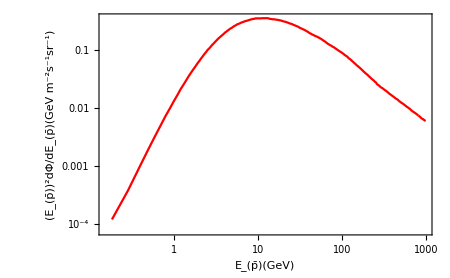

```mathematica
SumPlotifPoc1=ListLogLogPlot[Sumchar01,Joined->True,PlotStyle->Red,Frame->True,Axes->False,ImageSize->450 ,FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

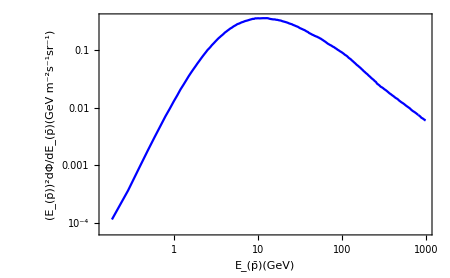

```mathematica
SumPlotifPoc2=ListLogLogPlot[Sumchar02,Joined->True,PlotStyle->Blue,Frame->True,Axes->False,ImageSize->450 ,FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

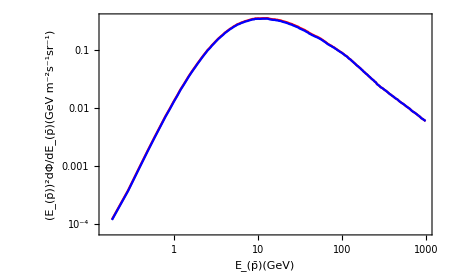

```mathematica
Show[SumPlotifPoc1,SumPlotifPoc2]
```

## χ^2- Fitting

```mathematica
Sumch1=Table[Sumchar01[IError1[[i,1]]],{i,Length[IError]}];
IErrorch1=Flatten[Table[{IError1[[i,2]]},{i,1,Length[IError]}],1];
IErrorSizech1=Flatten[Table[{IError1[[i,4]]},{i,1,Length[IError]}],1];
chiSUMch1=((Sumch1-IErrorch1)/IErrorSizech1)^2;
Sum[chiSUMch1[[i]],{i,1,Length[IError]}];
Sumch2=Table[Sumchar02[IError1[[i,1]]],{i,Length[IError]}];
IErrorch2=Flatten[Table[{IError1[[i,2]]},{i,1,Length[IError]}],1];
IErrorSizech2=Flatten[Table[{IError1[[i,4]]},{i,1,Length[IError]}],1];
chiSUMch2=((Sumch2-IErrorch2)/IErrorSizech2)^2;
Sum[chiSUMch2[[i]],{i,1,Length[IError]}];
```

## Mass-σv graph

```mathematica
ClearAll[τc02,mDM02]
```

```mathematica
τc02=10^lτc02;
mDM02=10^lmDM02;
```

```mathematica
Poτc2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryτc, haloτc, propagationτc][mDM02, τc02,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}]
Pobc2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primarybc, halobc, propagationbc][mDM02,3× (1/3)^2×τc02,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
Pocc2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primarycc, halocc, propagationcc][mDM02,3× (2/3)^2×τc02,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
Potc2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primarytc, halotc, propagationtc][mDM02,3× (2/3)^2×τc02,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
Poec2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryec, haloec, propagationec][mDM02,τc02,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
Poμc2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryμc, haloμc,propagationμc][mDM02, τc02,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
Poqc2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryqc, haloqc, propagationqc][mDM02,3× ((2/3)^2+(1/3)^2+(1/3)^2)×τc02,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}]

τctott=( 3+3× (1/3)^2+3× (2/3)^2+3× (2/3)^2+3× ((2/3)^2+(1/3)^2+(1/3)^2))

τctot=( 3+3× (1/3)^2+3× (2/3)^2+3× ((2/3)^2+(1/3)^2+(1/3)^2))
```

{{0.1,0.1 10.^If[0.1>10^lmDM02||10^lmDM02<1.777,-∞,Log10[10^lτc02/σvref]+tabΦpbarAnnI[τ,NFW,MED][10^lmDM02,-1.]]},399,{1000.,1000. 10.^If[1000.>10^lmDM02||10^lmDM02<1.777,-∞,Log10[10^lτc02/σvref]+tabΦpbarAnnI[τ,NFW,MED][10^lmDM02,3.]]}}
 |  |  |  |

{{0.1,0.1 10.^If[0.1>10^lmDM02||10^lmDM02<0,-∞,Log10[(2^(1+lτc02) 5^lτc02)/σvref]+tabΦpbarAnnI[q,NFW,MED][10^lmDM02,-1.]]},399,{1000.,1000. 10.^If[1000.>10^lmDM02||10^lmDM02<0,-∞,Log10[(2^(1+lτc02) 5^lτc02)/σvref]+tabΦpbarAnnI[q,NFW,MED][10^lmDM02,3.]]}}
 |  |  |  |

8

20/3

```mathematica
ifPoc3=Table[{Poμc2[[i,1]],(Poμc2[[i,2]]+Poec2[[i,2]]+Potc2[[i,2]]+Poτc2[[i,2]]+Pocc2[[i,2]]+Pobc2[[i,2]]+Poqc2[[i,2]])},{i,1,Length[Poμc2]}]
ifPoc3f=Interpolation[ifPoc3];
ifPoc4=Table[{Poμc2[[i,1]],(Poμc2[[i,2]]+Poec2[[i,2]]+Poτc2[[i,2]]+Pocc2[[i,2]]+Pobc2[[i,2]]+Poqc2[[i,2]])},{i,1,Length[Poμc2]}]
ifPoc4f=Interpolation[ifPoc4];
```

{{0.1,0.1 10.^If[0.1>10^lmDM02||10^lmDM02<0,-∞,Log10[(2^(1+lτc02) 5^lτc02)/σvref]+tabΦpbarAnnI[q,NFW,MED][10^lmDM02,-1.]]+0.1 10.^If[1]+0.1 10.^If[1]+0.1 10.^If[1]+0.1 10.^If[1]+0.1 10.^1+0.1 10.^If[0.1>10^lmDM02||10^lmDM02<175,-∞,Log10[(2^(2+5) 5^lτc02)/(3 σvref)]+tabΦpbarAnnI[t,NFW,MED][10^lmDM02,-1.]]},399,{1000.,1000. 10.^If[1]+5+1000. 10.^If[1]}}
 |  |  |  |

{{0.1,0.1 10.^If[0.1>10^lmDM02||10^lmDM02<0,-∞,Log10[(2^(1+lτc02) 5^lτc02)/σvref]+tabΦpbarAnnI[q,NFW,MED][10^lmDM02,-1.]]+0.1 10.^If[0.1>10^lmDM02||10^lmDM02<511/1000000,1,Log10[1/σvref]+1]+0.1 10.^If[1]+0.1 10.^If[1]+0.1 10.^If[1]+0.1 10.^If[0.1>10^lmDM02||10^lmDM02<5.1,-∞,Log10[10^lτc02/(3 σvref)]+tabΦpbarAnnI[b,NFW,MED][10^lmDM02,-1.]]},399,{1000.,1}}
 |  |  |  |

```mathematica
Sumchar03=Interpolation[Table[{x,ifBG0[x]+ifPoc3f[x]},{x,0.18,10^2.99,0.1}]];
Sumchar04=Interpolation[Table[{x,ifBG0[x]+ifPoc4f[x]},{x,0.18,10^2.99,0.1}]];
```

```mathematica
Sumch3=Table[Sumchar03[IError1[[i,1]]],{i,Length[IError]}];
chiSUMch03=((Sumch3-IErrorch1)/IErrorSizech1)^2;
FinalSumch03=Sum[chiSUMch03[[i]],{i,1,Length[IError]}];
Sumch4=Table[Sumchar04[IError1[[i,1]]],{i,Length[IError]}];
chiSUMch04=((Sumch4-IErrorch1)/IErrorSizech1)^2;
FinalSumch04=Sum[chiSUMch04[[i]],{i,1,Length[IError]}];
```

```mathematica
Log10[10^-25/(20./3)]
```

-25.8239

```mathematica
contchar1=Flatten[Table[{mDM02,Log[10,τctot *τc02],τctot*τc02,FinalSumch04},{lmDM02,0.7,Log10[topm],0.02},{lτc02,-28.82,-25.82,0.05}],1]
Export["contour_AMS_RED_char1.dat",contchar1,"Table"]

(*contchar1=Flatten[Table[{mDM02,Log[10,τctot *τc02],τctot*τc02,If[mDM02>Log10[173.21],FinalSumch03]},{lmDM02,0.7,2.4,0.05},{lτc02,-28.9,-25.9,0.05}],1]
Export["contour_AMS_char01.dat",contchar1,"Table"]*)

contchar2=Flatten[Table[{mDM02,Log[10,τctott *τc02],τctott*τc02,FinalSumch03},{lmDM02,Log10[topm],2.4,0.02},{lτc02,-28.90,-25.90,0.05}],1]
Export["contour_AMS_RED_char2.dat",contchar2,"Table"]
contchar3=Join[contchar1,contchar2]
Export["contour_AMS_RED_char3.dat",contchar3,"Table"]
```

{{5.01187,-27.9961,1.00904×10^-28,152.012},{5.01187,-27.9461,1.13216×10^-28,152.859},{5.01187,-27.8961,1.27031×10^-28,154.043},4691,{165.959,-25.0961,8.0151×10^-26,1574.62},{165.959,-25.0461,8.99309×10^-26,2022.35},{165.959,-24.9961,1.00904×10^-25,2595.69}}
 |  |  |  |

contour_AMS_RED_char1.dat

{{173.,-27.9969,1.00714×10^-28,151.869},{173.,-27.9469,1.13003×10^-28,151.799},{173.,-27.8969,1.26791×10^-28,151.72},{173.,-27.8469,1.42262×10^-28,151.632},{173.,-27.7969,1.59621×10^-28,151.533},{173.,-27.7469,1.79098×10^-28,151.422},{173.,-27.6969,2.00951×10^-28,151.297},{173.,-27.6469,2.25471×10^-28,151.158},{173.,-27.5969,2.52982×10^-28,151.002},{173.,-27.5469,2.83851×10^-28,150.828},{173.,-27.4969,3.18486×10^-28,150.632},{173.,-27.4469,3.57347×10^-28,150.414},{173.,-27.3969,4.0095×10^-28,150.169},{173.,-27.3469,4.49873×10^-28,149.896},{173.,-27.2969,5.04766×10^-28,149.59},{173.,-27.2469,5.66357×10^-28,149.248},{173.,-27.1969,6.35463×10^-28,148.866},{173.,-27.1469,7.13001×10^-28,148.441},{173.,-27.0969,8.×10^-28,147.966},{173.,-27.0469,8.97615×10^-28,147.436},{173.,-26.9969,1.00714×10^-27,146.847},{173.,-26.9469,1.13003×10^-27,146.192},{173.,-26.8969,1.26791×10^-27,145.464},{173.,-26.8469,1.42262×10^-27,144.656},{173.,-26.7969,1.59621×10^-27,143.761},{173.,-26.7469,1.79098×10^-27,142.771},{173.,-26.6969,2.00951×10^-27,141.678},{173.,-26.6469,2.25471×10^-27,140.475},{173.,-26.5969,2.52982×10^-27,139.154},{173.,-26.5469,2.83851×10^-27,137.708},{173.,-26.4969,3.18486×10^-27,136.132},{173.,-26.4469,3.57347×10^-27,134.42},{173.,-26.3969,4.0095×10^-27,132.571},{173.,-26.3469,4.49873×10^-27,130.588},{173.,-26.2969,5.04766×10^-27,128.478},{173.,-26.2469,5.66357×10^-27,126.254},{173.,-26.1969,6.35463×10^-27,123.94},{173.,-26.1469,7.13001×10^-27,121.572},{173.,-26.0969,8.×10^-27,119.203},{173.,-26.0469,8.97615×10^-27,116.907},{173.,-25.9969,1.00714×10^-26,114.787},{173.,-25.9469,1.13003×10^-26,112.982},{173.,-25.8969,1.26791×10^-26,111.679},{173.,-25.8469,1.42262×10^-26,111.127},{173.,-25.7969,1.59621×10^-26,111.652},{173.,-25.7469,1.79098×10^-26,113.683},{173.,-25.6969,2.00951×10^-26,117.776},{173.,-25.6469,2.25471×10^-26,124.653},{173.,-25.5969,2.52982×10^-26,135.246},{173.,-25.5469,2.83851×10^-26,150.752},{173.,-25.4969,3.18486×10^-26,172.708},{173.,-25.4469,3.57347×10^-26,203.081},{173.,-25.3969,4.0095×10^-26,244.385},{173.,-25.3469,4.49873×10^-26,299.824},{173.,-25.2969,5.04766×10^-26,373.478},{173.,-25.2469,5.66357×10^-26,470.533},{173.,-25.1969,6.35463×10^-26,597.578},{173.,-25.1469,7.13001×10^-26,762.969},{173.,-25.0969,8.×10^-26,977.303},{173.,-25.0469,8.97615×10^-26,1254.},{173.,-24.9969,1.00714×10^-25,1610.04},{181.153,-27.9969,1.00714×10^-28,151.767},{181.153,-27.9469,1.13003×10^-28,151.685},{181.153,-27.8969,1.26791×10^-28,151.592},{181.153,-27.8469,1.42262×10^-28,151.488},{181.153,-27.7969,1.59621×10^-28,151.372},{181.153,-27.7469,1.79098×10^-28,151.241},{181.153,-27.6969,2.00951×10^-28,151.095},{181.153,-27.6469,2.25471×10^-28,150.931},{181.153,-27.5969,2.52982×10^-28,150.748},{181.153,-27.5469,2.83851×10^-28,150.543},{181.153,-27.4969,3.18486×10^-28,150.313},{181.153,-27.4469,3.57347×10^-28,150.056},{181.153,-27.3969,4.0095×10^-28,149.768},{181.153,-27.3469,4.49873×10^-28,149.446},{181.153,-27.2969,5.04766×10^-28,149.087},{181.153,-27.2469,5.66357×10^-28,148.685},{181.153,-27.1969,6.35463×10^-28,148.236},{181.153,-27.1469,7.13001×10^-28,147.735},{181.153,-27.0969,8.×10^-28,147.176},{181.153,-27.0469,8.97615×10^-28,146.554},{181.153,-26.9969,1.00714×10^-27,145.861},{181.153,-26.9469,1.13003×10^-27,145.09},{181.153,-26.8969,1.26791×10^-27,144.233},{181.153,-26.8469,1.42262×10^-27,143.283},{181.153,-26.7969,1.59621×10^-27,142.23},{181.153,-26.7469,1.79098×10^-27,141.065},{181.153,-26.6969,2.00951×10^-27,139.78},{181.153,-26.6469,2.25471×10^-27,138.364},{181.153,-26.5969,2.52982×10^-27,136.81},{181.153,-26.5469,2.83851×10^-27,135.108},{181.153,-26.4969,3.18486×10^-27,133.252},{181.153,-26.4469,3.57347×10^-27,131.237},{181.153,-26.3969,4.0095×10^-27,129.06},{181.153,-26.3469,4.49873×10^-27,126.725},{181.153,-26.2969,5.04766×10^-27,124.239},{181.153,-26.2469,5.66357×10^-27,121.618},{181.153,-26.1969,6.35463×10^-27,118.89},{181.153,-26.1469,7.13001×10^-27,116.098},{181.153,-26.0969,8.×10^-27,113.301},{181.153,-26.0469,8.97615×10^-27,110.588},{181.153,-25.9969,1.00714×10^-26,108.077},{181.153,-25.9469,1.13003×10^-26,105.933},{181.153,-25.8969,1.26791×10^-26,104.375},{181.153,-25.8469,1.42262×10^-26,103.691},{181.153,-25.7969,1.59621×10^-26,104.266},{181.153,-25.7469,1.79098×10^-26,106.601},{181.153,-25.6969,2.00951×10^-26,111.348},{181.153,-25.6469,2.25471×10^-26,119.35},{181.153,-25.5969,2.52982×10^-26,131.7},{181.153,-25.5469,2.83851×10^-26,149.801},{181.153,-25.4969,3.18486×10^-26,175.452},{181.153,-25.4469,3.57347×10^-26,210.958},{181.153,-25.3969,4.0095×10^-26,259.264},{181.153,-25.3469,4.49873×10^-26,324.122},{181.153,-25.2969,5.04766×10^-26,410.313},{181.153,-25.2469,5.66357×10^-26,523.915},{181.153,-25.1969,6.35463×10^-26,672.645},{181.153,-25.1469,7.13001×10^-26,866.297},{181.153,-25.0969,8.×10^-26,1117.28},{181.153,-25.0469,8.97615×10^-26,1441.33},{181.153,-24.9969,1.00714×10^-25,1858.34},{189.691,-27.9969,1.00714×10^-28,151.804},{189.691,-27.9469,1.13003×10^-28,151.726},{189.691,-27.8969,1.26791×10^-28,151.638},{189.691,-27.8469,1.42262×10^-28,151.54},{189.691,-27.7969,1.59621×10^-28,151.429},{189.691,-27.7469,1.79098×10^-28,151.306},{189.691,-27.6969,2.00951×10^-28,151.168},{189.691,-27.6469,2.25471×10^-28,151.013},{189.691,-27.5969,2.52982×10^-28,150.839},{189.691,-27.5469,2.83851×10^-28,150.645},{189.691,-27.4969,3.18486×10^-28,150.427},{189.691,-27.4469,3.57347×10^-28,150.184},{189.691,-27.3969,4.0095×10^-28,149.911},{189.691,-27.3469,4.49873×10^-28,149.606},{189.691,-27.2969,5.04766×10^-28,149.266},{189.691,-27.2469,5.66357×10^-28,148.885},{189.691,-27.1969,6.35463×10^-28,148.46},{189.691,-27.1469,7.13001×10^-28,147.986},{189.691,-27.0969,8.×10^-28,147.456},{189.691,-27.0469,8.97615×10^-28,146.866},{189.691,-26.9969,1.00714×10^-27,146.209},{189.691,-26.9469,1.13003×10^-27,145.479},{189.691,-26.8969,1.26791×10^-27,144.666},{189.691,-26.8469,1.42262×10^-27,143.765},{189.691,-26.7969,1.59621×10^-27,142.766},{189.691,-26.7469,1.79098×10^-27,141.66},{189.691,-26.6969,2.00951×10^-27,140.439},{189.691,-26.6469,2.25471×10^-27,139.094},{189.691,-26.5969,2.52982×10^-27,137.617},{189.691,-26.5469,2.83851×10^-27,135.998},{189.691,-26.4969,3.18486×10^-27,134.23},{189.691,-26.4469,3.57347×10^-27,132.31},{189.691,-26.3969,4.0095×10^-27,130.233},{189.691,-26.3469,4.49873×10^-27,128.001},{189.691,-26.2969,5.04766×10^-27,125.621},{189.691,-26.2469,5.66357×10^-27,123.107},{189.691,-26.1969,6.35463×10^-27,120.482},{189.691,-26.1469,7.13001×10^-27,117.785},{189.691,-26.0969,8.×10^-27,115.07},{189.691,-26.0469,8.97615×10^-27,112.416},{189.691,-25.9969,1.00714×10^-26,109.931},{189.691,-25.9469,1.13003×10^-26,107.765},{189.691,-25.8969,1.26791×10^-26,106.117},{189.691,-25.8469,1.42262×10^-26,105.252},{189.691,-25.7969,1.59621×10^-26,105.522},{189.691,-25.7469,1.79098×10^-26,107.386},{189.691,-25.6969,2.00951×10^-26,111.442},{189.691,-25.6469,2.25471×10^-26,118.468},{189.691,-25.5969,2.52982×10^-26,129.465},{189.691,-25.5469,2.83851×10^-26,145.725},{189.691,-25.4969,3.18486×10^-26,168.906},{189.691,-25.4469,3.57347×10^-26,201.129},{189.691,-25.3969,4.0095×10^-26,245.108},{189.691,-25.3469,4.49873×10^-26,304.302},{189.691,-25.2969,5.04766×10^-26,383.118},{189.691,-25.2469,5.66357×10^-26,487.161},{189.691,-25.1969,6.35463×10^-26,623.551},{189.691,-25.1469,7.13001×10^-26,801.322},{189.691,-25.0969,8.×10^-26,1031.93},{189.691,-25.0469,8.97615×10^-26,1329.89},{189.691,-24.9969,1.00714×10^-25,1713.56},{198.631,-27.9969,1.00714×10^-28,151.838},{198.631,-27.9469,1.13003×10^-28,151.764},{198.631,-27.8969,1.26791×10^-28,151.681},{198.631,-27.8469,1.42262×10^-28,151.588},{198.631,-27.7969,1.59621×10^-28,151.484},{198.631,-27.7469,1.79098×10^-28,151.367},{198.631,-27.6969,2.00951×10^-28,151.236},{198.631,-27.6469,2.25471×10^-28,151.09},{198.631,-27.5969,2.52982×10^-28,150.925},{198.631,-27.5469,2.83851×10^-28,150.741},{198.631,-27.4969,3.18486×10^-28,150.535},{198.631,-27.4469,3.57347×10^-28,150.305},{198.631,-27.3969,4.0095×10^-28,150.047},{198.631,-27.3469,4.49873×10^-28,149.758},{198.631,-27.2969,5.04766×10^-28,149.436},{198.631,-27.2469,5.66357×10^-28,149.076},{198.631,-27.1969,6.35463×10^-28,148.673},{198.631,-27.1469,7.13001×10^-28,148.223},{198.631,-27.0969,8.×10^-28,147.722},{198.631,-27.0469,8.97615×10^-28,147.163},{198.631,-26.9969,1.00714×10^-27,146.541},{198.631,-26.9469,1.13003×10^-27,145.848},{198.631,-26.8969,1.26791×10^-27,145.078},{198.631,-26.8469,1.42262×10^-27,144.223},{198.631,-26.7969,1.59621×10^-27,143.275},{198.631,-26.7469,1.79098×10^-27,142.226},{198.631,-26.6969,2.00951×10^-27,141.068},{198.631,-26.6469,2.25471×10^-27,139.79},{198.631,-26.5969,2.52982×10^-27,138.386},{198.631,-26.5469,2.83851×10^-27,136.847},{198.631,-26.4969,3.18486×10^-27,135.166},{198.631,-26.4469,3.57347×10^-27,133.337},{198.631,-26.3969,4.0095×10^-27,131.357},{198.631,-26.3469,4.49873×10^-27,129.227},{198.631,-26.2969,5.04766×10^-27,126.952},{198.631,-26.2469,5.66357×10^-27,124.543},{198.631,-26.1969,6.35463×10^-27,122.023},{198.631,-26.1469,7.13001×10^-27,119.425},{198.631,-26.0969,8.×10^-27,116.797},{198.631,-26.0469,8.97615×10^-27,114.212},{198.631,-25.9969,1.00714×10^-26,111.769},{198.631,-25.9469,1.13003×10^-26,109.602},{198.631,-25.8969,1.26791×10^-26,107.896},{198.631,-25.8469,1.42262×10^-26,106.893},{198.631,-25.7969,1.59621×10^-26,106.916},{198.631,-25.7469,1.79098×10^-26,108.387},{198.631,-25.6969,2.00951×10^-26,111.857},{198.631,-25.6469,2.25471×10^-26,118.04},{198.631,-25.5969,2.52982×10^-26,127.861},{198.631,-25.5469,2.83851×10^-26,142.511},{198.631,-25.4969,3.18486×10^-26,163.518},{198.631,-25.4469,3.57347×10^-26,192.842},{198.631,-25.3969,4.0095×10^-26,232.986},{198.631,-25.3469,4.49873×10^-26,287.148},{198.631,-25.2969,5.04766×10^-26,359.397},{198.631,-25.2469,5.66357×10^-26,454.913},{198.631,-25.1969,6.35463×10^-26,580.277},{198.631,-25.1469,7.13001×10^-26,743.842},{198.631,-25.0969,8.×10^-26,956.199},{198.631,-25.0469,8.97615×10^-26,1230.77},{198.631,-24.9969,1.00714×10^-25,1584.54},{207.992,-27.9969,1.00714×10^-28,151.869},{207.992,-27.9469,1.13003×10^-28,151.799},{207.992,-27.8969,1.26791×10^-28,151.72},{207.992,-27.8469,1.42262×10^-28,151.632},{207.992,-27.7969,1.59621×10^-28,151.533},{207.992,-27.7469,1.79098×10^-28,151.422},{207.992,-27.6969,2.00951×10^-28,151.297},{207.992,-27.6469,2.25471×10^-28,151.158},{207.992,-27.5969,2.52982×10^-28,151.002},{207.992,-27.5469,2.83851×10^-28,150.827},{207.992,-27.4969,3.18486×10^-28,150.632},{207.992,-27.4469,3.57347×10^-28,150.413},{207.992,-27.3969,4.0095×10^-28,150.168},{207.992,-27.3469,4.49873×10^-28,149.894},{207.992,-27.2969,5.04766×10^-28,149.587},{207.992,-27.2469,5.66357×10^-28,149.245},{207.992,-27.1969,6.35463×10^-28,148.862},{207.992,-27.1469,7.13001×10^-28,148.435},{207.992,-27.0969,8.×10^-28,147.958},{207.992,-27.0469,8.97615×10^-28,147.426},{207.992,-26.9969,1.00714×10^-27,146.834},{207.992,-26.9469,1.13003×10^-27,146.175},{207.992,-26.8969,1.26791×10^-27,145.442},{207.992,-26.8469,1.42262×10^-27,144.629},{207.992,-26.7969,1.59621×10^-27,143.726},{207.992,-26.7469,1.79098×10^-27,142.727},{207.992,-26.6969,2.00951×10^-27,141.622},{207.992,-26.6469,2.25471×10^-27,140.404},{207.992,-26.5969,2.52982×10^-27,139.064},{207.992,-26.5469,2.83851×10^-27,137.594},{207.992,-26.4969,3.18486×10^-27,135.987},{207.992,-26.4469,3.57347×10^-27,134.236},{207.992,-26.3969,4.0095×10^-27,132.339},{207.992,-26.3469,4.49873×10^-27,130.295},{207.992,-26.2969,5.04766×10^-27,128.107},{207.992,-26.2469,5.66357×10^-27,125.785},{207.992,-26.1969,6.35463×10^-27,123.348},{207.992,-26.1469,7.13001×10^-27,120.825},{207.992,-26.0969,8.×10^-27,118.261},{207.992,-26.0469,8.97615×10^-27,115.718},{207.992,-25.9969,1.00714×10^-26,113.287},{207.992,-25.9469,1.13003×10^-26,111.09},{207.992,-25.8969,1.26791×10^-26,109.294},{207.992,-25.8469,1.42262×10^-26,108.119},{207.992,-25.7969,1.59621×10^-26,107.861},{207.992,-25.7469,1.79098×10^-26,108.905},{207.992,-25.6969,2.00951×10^-26,111.756},{207.992,-25.6469,2.25471×10^-26,117.068},{207.992,-25.5969,2.52982×10^-26,125.689},{207.992,-25.5469,2.83851×10^-26,138.712},{207.992,-25.4969,3.18486×10^-26,157.542},{207.992,-25.4469,3.57347×10^-26,183.979},{207.992,-25.3969,4.0095×10^-26,220.325},{207.992,-25.3469,4.49873×10^-26,269.522},{207.992,-25.2969,5.04766×10^-26,335.315},{207.992,-25.2469,5.66357×10^-26,422.472},{207.992,-25.1969,6.35463×10^-26,537.054},{207.992,-25.1469,7.13001×10^-26,686.755},{207.992,-25.0969,8.×10^-26,881.332},{207.992,-25.0469,8.97615×10^-26,1133.15},{207.992,-24.9969,1.00714×10^-25,1457.87},{217.794,-27.9969,1.00714×10^-28,151.899},{217.794,-27.9469,1.13003×10^-28,151.833},{217.794,-27.8969,1.26791×10^-28,151.758},{217.794,-27.8469,1.42262×10^-28,151.674},{217.794,-27.7969,1.59621×10^-28,151.58},{217.794,-27.7469,1.79098×10^-28,151.475},{217.794,-27.6969,2.00951×10^-28,151.357},{217.794,-27.6469,2.25471×10^-28,151.225},{217.794,-27.5969,2.52982×10^-28,151.077},{217.794,-27.5469,2.83851×10^-28,150.911},{217.794,-27.4969,3.18486×10^-28,150.726},{217.794,-27.4469,3.57347×10^-28,150.518},{217.794,-27.3969,4.0095×10^-28,150.286},{217.794,-27.3469,4.49873×10^-28,150.026},{217.794,-27.2969,5.04766×10^-28,149.735},{217.794,-27.2469,5.66357×10^-28,149.41},{217.794,-27.1969,6.35463×10^-28,149.047},{217.794,-27.1469,7.13001×10^-28,148.641},{217.794,-27.0969,8.×10^-28,148.189},{217.794,-27.0469,8.97615×10^-28,147.684},{217.794,-26.9969,1.00714×10^-27,147.122},{217.794,-26.9469,1.13003×10^-27,146.496},{217.794,-26.8969,1.26791×10^-27,145.8},{217.794,-26.8469,1.42262×10^-27,145.026},{217.794,-26.7969,1.59621×10^-27,144.168},{217.794,-26.7469,1.79098×10^-27,143.218},{217.794,-26.6969,2.00951×10^-27,142.167},{217.794,-26.6469,2.25471×10^-27,141.007},{217.794,-26.5969,2.52982×10^-27,139.731},{217.794,-26.5469,2.83851×10^-27,138.329},{217.794,-26.4969,3.18486×10^-27,136.796},{217.794,-26.4469,3.57347×10^-27,135.124},{217.794,-26.3969,4.0095×10^-27,133.31},{217.794,-26.3469,4.49873×10^-27,131.352},{217.794,-26.2969,5.04766×10^-27,129.253},{217.794,-26.2469,5.66357×10^-27,127.021},{217.794,-26.1969,6.35463×10^-27,124.671},{217.794,-26.1469,7.13001×10^-27,122.229},{217.794,-26.0969,8.×10^-27,119.735},{217.794,-26.0469,8.97615×10^-27,117.246},{217.794,-25.9969,1.00714×10^-26,114.841},{217.794,-25.9469,1.13003×10^-26,112.633},{217.794,-25.8969,1.26791×10^-26,110.772},{217.794,-25.8469,1.42262×10^-26,109.46},{217.794,-25.7969,1.59621×10^-26,108.964},{217.794,-25.7469,1.79098×10^-26,109.638},{217.794,-25.6969,2.00951×10^-26,111.942},{217.794,-25.6469,2.25471×10^-26,116.476},{217.794,-25.5969,2.52982×10^-26,124.018},{217.794,-25.5469,2.83851×10^-26,135.569},{217.794,-25.4969,3.18486×10^-26,152.418},{217.794,-25.4469,3.57347×10^-26,176.219},{217.794,-25.3969,4.0095×10^-26,209.089},{217.794,-25.3469,4.49873×10^-26,253.728},{217.794,-25.2969,5.04766×10^-26,313.583},{217.794,-25.2469,5.66357×10^-26,393.04},{217.794,-25.1969,6.35463×10^-26,497.674},{217.794,-25.1469,7.13001×10^-26,634.567},{217.794,-25.0969,8.×10^-26,812.702},{217.794,-25.0469,8.97615×10^-26,1043.46},{217.794,-24.9969,1.00714×10^-25,1341.27},{228.058,-27.9969,1.00714×10^-28,151.927},{228.058,-27.9469,1.13003×10^-28,151.864},{228.058,-27.8969,1.26791×10^-28,151.793},{228.058,-27.8469,1.42262×10^-28,151.714},{228.058,-27.7969,1.59621×10^-28,151.625},{228.058,-27.7469,1.79098×10^-28,151.525},{228.058,-27.6969,2.00951×10^-28,151.413},{228.058,-27.6469,2.25471×10^-28,151.288},{228.058,-27.5969,2.52982×10^-28,151.147},{228.058,-27.5469,2.83851×10^-28,150.99},{228.058,-27.4969,3.18486×10^-28,150.814},{228.058,-27.4469,3.57347×10^-28,150.617},{228.058,-27.3969,4.0095×10^-28,150.396},{228.058,-27.3469,4.49873×10^-28,150.149},{228.058,-27.2969,5.04766×10^-28,149.873},{228.058,-27.2469,5.66357×10^-28,149.565},{228.058,-27.1969,6.35463×10^-28,149.22},{228.058,-27.1469,7.13001×10^-28,148.835},{228.058,-27.0969,8.×10^-28,148.405},{228.058,-27.0469,8.97615×10^-28,147.926},{228.058,-26.9969,1.00714×10^-27,147.391},{228.058,-26.9469,1.13003×10^-27,146.796},{228.058,-26.8969,1.26791×10^-27,146.135},{228.058,-26.8469,1.42262×10^-27,145.399},{228.058,-26.7969,1.59621×10^-27,144.583},{228.058,-26.7469,1.79098×10^-27,143.678},{228.058,-26.6969,2.00951×10^-27,142.677},{228.058,-26.6469,2.25471×10^-27,141.572},{228.058,-26.5969,2.52982×10^-27,140.355},{228.058,-26.5469,2.83851×10^-27,139.017},{228.058,-26.4969,3.18486×10^-27,137.553},{228.058,-26.4469,3.57347×10^-27,135.954},{228.058,-26.3969,4.0095×10^-27,134.217},{228.058,-26.3469,4.49873×10^-27,132.34},{228.058,-26.2969,5.04766×10^-27,130.323},{228.058,-26.2469,5.66357×10^-27,128.173},{228.058,-26.1969,6.35463×10^-27,125.903},{228.058,-26.1469,7.13001×10^-27,123.536},{228.058,-26.0969,8.×10^-27,121.106},{228.058,-26.0469,8.97615×10^-27,118.663},{228.058,-25.9969,1.00714×10^-26,116.279},{228.058,-25.9469,1.13003×10^-26,114.055},{228.058,-25.8969,1.26791×10^-26,112.126},{228.058,-25.8469,1.42262×10^-26,110.676},{228.058,-25.7969,1.59621×10^-26,109.947},{228.058,-25.7469,1.79098×10^-26,110.26},{228.058,-25.6969,2.00951×10^-26,112.035},{228.058,-25.6469,2.25471×10^-26,115.819},{228.058,-25.5969,2.52982×10^-26,122.321},{228.058,-25.5469,2.83851×10^-26,132.457},{228.058,-25.4969,3.18486×10^-26,147.407},{228.058,-25.4469,3.57347×10^-26,168.683},{228.058,-25.3969,4.0095×10^-26,198.223},{228.058,-25.3469,4.49873×10^-26,238.503},{228.058,-25.2969,5.04766×10^-26,292.682},{228.058,-25.2469,5.66357×10^-26,364.782},{228.058,-25.1969,6.35463×10^-26,459.916},{228.058,-25.1469,7.13001×10^-26,584.583},{228.058,-25.0969,8.×10^-26,747.027},{228.058,-25.0469,8.97615×10^-26,957.7},{228.058,-24.9969,1.00714×10^-25,1229.84},{238.806,-27.9969,1.00714×10^-28,151.954},{238.806,-27.9469,1.13003×10^-28,151.895},{238.806,-27.8969,1.26791×10^-28,151.827},{238.806,-27.8469,1.42262×10^-28,151.752},{238.806,-27.7969,1.59621×10^-28,151.668},{238.806,-27.7469,1.79098×10^-28,151.573},{238.806,-27.6969,2.00951×10^-28,151.467},{238.806,-27.6469,2.25471×10^-28,151.348},{238.806,-27.5969,2.52982×10^-28,151.215},{238.806,-27.5469,2.83851×10^-28,151.066},{238.806,-27.4969,3.18486×10^-28,150.899},{238.806,-27.4469,3.57347×10^-28,150.712},{238.806,-27.3969,4.0095×10^-28,150.502},{238.806,-27.3469,4.49873×10^-28,150.268},{238.806,-27.2969,5.04766×10^-28,150.006},{238.806,-27.2469,5.66357×10^-28,149.714},{238.806,-27.1969,6.35463×10^-28,149.386},{238.806,-27.1469,7.13001×10^-28,149.021},{238.806,-27.0969,8.×10^-28,148.613},{238.806,-27.0469,8.97615×10^-28,148.158},{238.806,-26.9969,1.00714×10^-27,147.65},{238.806,-26.9469,1.13003×10^-27,147.085},{238.806,-26.8969,1.26791×10^-27,146.456},{238.806,-26.8469,1.42262×10^-27,145.757},{238.806,-26.7969,1.59621×10^-27,144.98},{238.806,-26.7469,1.79098×10^-27,144.12},{238.806,-26.6969,2.00951×10^-27,143.167},{238.806,-26.6469,2.25471×10^-27,142.115},{238.806,-26.5969,2.52982×10^-27,140.955},{238.806,-26.5469,2.83851×10^-27,139.679},{238.806,-26.4969,3.18486×10^-27,138.281},{238.806,-26.4469,3.57347×10^-27,136.753},{238.806,-26.3969,4.0095×10^-27,135.091},{238.806,-26.3469,4.49873×10^-27,133.292},{238.806,-26.2969,5.04766×10^-27,131.356},{238.806,-26.2469,5.66357×10^-27,129.287},{238.806,-26.1969,6.35463×10^-27,127.097},{238.806,-26.1469,7.13001×10^-27,124.804},{238.806,-26.0969,8.×10^-27,122.438},{238.806,-26.0469,8.97615×10^-27,120.044},{238.806,-25.9969,1.00714×10^-26,117.687},{238.806,-25.9469,1.13003×10^-26,115.456},{238.806,-25.8969,1.26791×10^-26,113.472},{238.806,-25.8469,1.42262×10^-26,111.902},{238.806,-25.7969,1.59621×10^-26,110.965},{238.806,-25.7469,1.79098×10^-26,110.952},{238.806,-25.6969,2.00951×10^-26,112.244},{238.806,-25.6469,2.25471×10^-26,115.34},{238.806,-25.5969,2.52982×10^-26,120.885},{238.806,-25.5469,2.83851×10^-26,129.715},{238.806,-25.4969,3.18486×10^-26,142.906},{238.806,-25.4469,3.57347×10^-26,161.84},{238.806,-25.3969,4.0095×10^-26,188.289},{238.806,-25.3469,4.49873×10^-26,224.516},{238.806,-25.2969,5.04766×10^-26,273.411},{238.806,-25.2469,5.66357×10^-26,338.656},{238.806,-25.1969,6.35463×10^-26,424.934},{238.806,-25.1469,7.13001×10^-26,538.196},{238.806,-25.0969,8.×10^-26,685.995},{238.806,-25.0469,8.97615×10^-26,877.91},{238.806,-24.9969,1.00714×10^-25,1126.08},{250.061,-27.9969,1.00714×10^-28,151.98},{250.061,-27.9469,1.13003×10^-28,151.923},{250.061,-27.8969,1.26791×10^-28,151.859},{250.061,-27.8469,1.42262×10^-28,151.787},{250.061,-27.7969,1.59621×10^-28,151.707},{250.061,-27.7469,1.79098×10^-28,151.617},{250.061,-27.6969,2.00951×10^-28,151.517},{250.061,-27.6469,2.25471×10^-28,151.404},{250.061,-27.5969,2.52982×10^-28,151.277},{250.061,-27.5469,2.83851×10^-28,151.136},{250.061,-27.4969,3.18486×10^-28,150.977},{250.061,-27.4469,3.57347×10^-28,150.8},{250.061,-27.3969,4.0095×10^-28,150.601},{250.061,-27.3469,4.49873×10^-28,150.379},{250.061,-27.2969,5.04766×10^-28,150.13},{250.061,-27.2469,5.66357×10^-28,149.852},{250.061,-27.1969,6.35463×10^-28,149.541},{250.061,-27.1469,7.13001×10^-28,149.194},{250.061,-27.0969,8.×10^-28,148.806},{250.061,-27.0469,8.97615×10^-28,148.373},{250.061,-26.9969,1.00714×10^-27,147.891},{250.061,-26.9469,1.13003×10^-27,147.353},{250.061,-26.8969,1.26791×10^-27,146.755},{250.061,-26.8469,1.42262×10^-27,146.089},{250.061,-26.7969,1.59621×10^-27,145.35},{250.061,-26.7469,1.79098×10^-27,144.531},{250.061,-26.6969,2.00951×10^-27,143.623},{250.061,-26.6469,2.25471×10^-27,142.62},{250.061,-26.5969,2.52982×10^-27,141.513},{250.061,-26.5469,2.83851×10^-27,140.295},{250.061,-26.4969,3.18486×10^-27,138.959},{250.061,-26.4469,3.57347×10^-27,137.497},{250.061,-26.3969,4.0095×10^-27,135.905},{250.061,-26.3469,4.49873×10^-27,134.179},{250.061,-26.2969,5.04766×10^-27,132.318},{250.061,-26.2469,5.66357×10^-27,130.325},{250.061,-26.1969,6.35463×10^-27,128.208},{250.061,-26.1469,7.13001×10^-27,125.985},{250.061,-26.0969,8.×10^-27,123.68},{250.061,-26.0469,8.97615×10^-27,121.333},{250.061,-25.9969,1.00714×10^-26,119.001},{250.061,-25.9469,1.13003×10^-26,116.764},{250.061,-25.8969,1.26791×10^-26,114.732},{250.061,-25.8469,1.42262×10^-26,113.052},{250.061,-25.7969,1.59621×10^-26,111.924},{250.061,-25.7469,1.79098×10^-26,111.611},{250.061,-25.6969,2.00951×10^-26,112.459},{250.061,-25.6469,2.25471×10^-26,114.921},{250.061,-25.5969,2.52982×10^-26,119.583},{250.061,-25.5469,2.83851×10^-26,127.208},{250.061,-25.4969,3.18486×10^-26,138.775},{250.061,-25.4469,3.57347×10^-26,155.545},{250.061,-25.3969,4.0095×10^-26,179.137},{250.061,-25.3469,4.49873×10^-26,211.617},{250.061,-25.2969,5.04766×10^-26,255.628},{250.061,-25.2469,5.66357×10^-26,314.535},{250.061,-25.1969,6.35463×10^-26,392.622},{250.061,-25.1469,7.13001×10^-26,495.335},{250.061,-25.0969,8.×10^-26,629.588},{250.061,-25.0469,8.97615×10^-26,804.151},{250.061,-24.9969,1.00714×10^-25,1030.14}}

contour_AMS_RED_char2.dat

{{5.01187,-27.9961,1.00904×10^-28,152.012},{5.01187,-27.9461,1.13216×10^-28,152.859},{5.01187,-27.8961,1.27031×10^-28,154.043},5240,{250.061,-25.0969,8.×10^-26,629.588},{250.061,-25.0469,8.97615×10^-26,804.151},{250.061,-24.9969,1.00714×10^-25,1030.14}}
 |  |  |  |

contour_AMS_RED_char3.dat

```mathematica
contchar01=Import["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_charge/contour_AMS_RED_char1.dat","Table",HeaderLines->1];
contchar02=Import["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_charge/contour_AMS_RED_char2.dat","Table",HeaderLines->1];
contchar03=Import["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_charge/contour_AMS_RED_char3.dat","Table",HeaderLines->1];
```

```mathematica
contcharLog01=Table[{contchar01[[i,1]],contchar01[[i,2]],contchar01[[i, 4]]},{i, Length[contchar01]}];
contcharLog02=Table[{contchar02[[i,1]],contchar02[[i,2]],contchar02[[i, 4]]},{i, Length[contchar02]}];
contcharLog03=Table[{contchar03[[i,1]],contchar03[[i,2]], contchar03[[i, 4]]},{i, Length[contchar03]}];
```

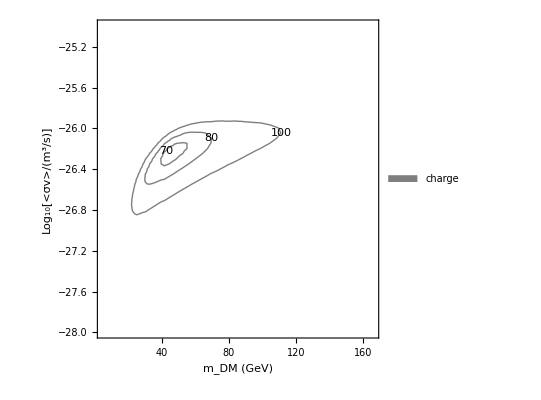

```mathematica
ListContourPlot[contcharLog01,Contours-> {60, 65,70,80,100},
 FrameLabel->{"m_DM (GeV)","Log_10[<σv>/(m^3/s)]"}, ContourLabels->All,ContourShading->None,ContourStyle->{Black},PlotLegends->Placed[SwatchLegend[{"charge"},LegendMarkerSize->20],Right]]
```